```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Block[
{f,r,l},
f[r_,l_]:=1+r^2/l^2;
EulerEquations[q/r[t]-Sqrt[-r'[t]^2/f[r[t],l]+f[r[t],l]],r[t],t]
]
```

(2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t]))/(l^2 r[t]^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0

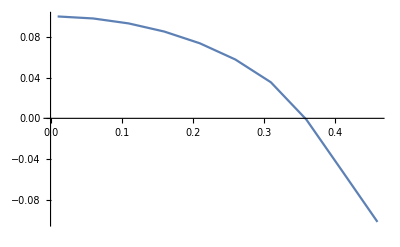

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{i,fr[1,0.1,i,0.1 qcrit[1,0.1]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

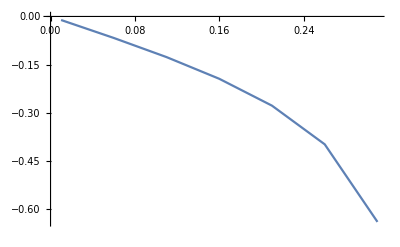

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{i,pr[1,0.1,i,0.1 qcrit[1,0.1]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{fr[1,0.1,i,0.1qcrit[1,0.1]],pr[1,0.1,i,0.1 qcrit[1,0.1]]},{i,0.01,20,0.1}],AxesOrigin->{0,0}]];
]
```

NDSolveValue::mxst: Maximum number of 97422 steps reached at the point t == 16.0667.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

$Aborted

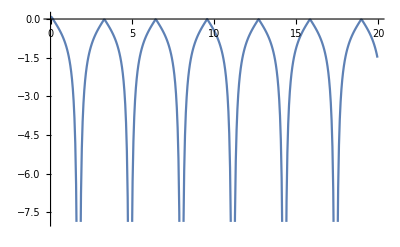

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{i,fr[1,0.1,i,1.4 qcrit[1,0.1]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

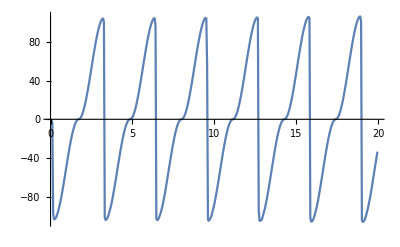

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{i,pr[1,0.1,i,1.4 qcrit[1,0.1]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

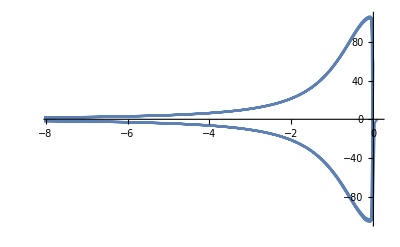

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{fr[1,0.1,i,1.4 qcrit[1,0.1]],pr[1,0.1,i,1.4 qcrit[1,0.1]]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

```mathematica
(*M=0 SAdS*)
```